# rydberg-rydberg interactions

P. Huft

```mathematica
SetDirectory[NotebookDirectory[]];
```

## general setup

```mathematica
(*CONSTANTS*)
ℏ=1;
ee= 1.602*^-19;
c = 3*10^8;
μ0 =4π*10^-7;
ϵ0 = 1/√(c μ0);
qq = ee^2/(4 π ϵ0);

(*FUNCTIONS*)
OuterProd[A_,B_]:=Outer[Times,A,B]; (*outer product of vectors or matrices A,B*)
HamiltonianProduct[hsingle_,volume_ ]:=Module[
{totalham=hsingle},
(*the Hamiltonian describing the combined space of `volume` number of quantum systems with individual Hamiltonian hsingle*)
For[i=1,i<volume,i++,
totalham = KroneckerProduct[IdentityMatrix[Length[hsingle]],totalham] + KroneckerProduct[hsingle,IdentityMatrix[Length[totalham]]];
];
totalham
];

(*the total blockade to an n-Rydberg excited state due to the atoms participating*)
BlockadeTerm[atomIdcs_,blockadeTwoAtoms_]:=Total[Flatten@Table[blockadeTwoAtoms[atomIdcs[[i]],atomIdcs[[j]]],{i,Range[Length[atomIdcs]]},{j,Range[1+i,Length[atomIdcs]]}]]
BlockadeHamiltonian[atomNum_,blockade_]:=Module[
{excitedList={0,1},n,HBlockade},
(*blockade is a function that takes a list of atom indices (1,2...) and return the corresponding blockade between atoms*)

(*generate list of Rydberg-excited atoms at each index of the basis. for now, this assumes a system of two-level atoms*)
For[i=1,i<atomNum,i++,
n=(Flatten@excitedList)[[-1]]+1;
AppendTo[excitedList,n];
oldLength = Length[excitedList];
For[j=2,j<oldLength,j++,
AppendTo[excitedList,Flatten@{excitedList[[j]],n}];
];
];

dim = 2^atomNum;
HBlockade = ConstantArray[0,{dim,dim}];
For[k=1,k<dim+1,k++,
atoms = excitedList[[k]];
HBlockade[[k,k]]=If[Length[atoms]>0,blockade[atoms],0];
];
HBlockade
];
ΩBString[i_,j_]:=StringForm["Ω_B^(``, ``)",i,j];
```

## single Rydberg state

### algebra

Single atom dipole matrix elements to be computed with PairInteraction module in python.

Single atom structure: include two ground states, intermediate excited state, Rydberg state. Assume that large Zeeman shifts isolate an effective 4 level lambda system.

Matrix elems. reshape H into atoms*states x atoms*states. 
H_(4 atomi - statei+1,4atomj-statej+1)=Δ_g1 δ_ij δ_(statei,1)δ_(statej,1)+Δ_g2 δ_ij δ_(statei,2)δ_(statej,2)+Δ_e δ_ij δ_(statei,3)δ_(statej,3)+ℏΩ_(1A)(δ_ij δ_(statei,2)δ_(statej,3)+δ_ij δ_(statei,3)δ_(statej,2))/2+ℏΩ_(1B)(δ_ij δ_(statei,1)δ_(statej,3)+δ_ij δ_(statei,3)δ_(statej,1))/2+ℏΩ_2(δ_ij δ_(statei,3)δ_(statej,4)+δ_ij δ_(statei,4)δ_(statej,3))/2+ (1-δ_ij)δ_(statei,4)δ_(statej,4)Vdd
Computationally more friendly to define a matrix Hij that describes the energy levels and coupling scheme of atom i, plus the interactions to atom j. Then just build Hfull by iterating over Hfull and plopping in Hij at each section atom x atom section.hmmm this is mixing a single atom basis with a two-atom basis... doesn’t really make sense as framed.

```mathematica
Hi =({{0, 0, Ω1B, 0}, {0, Δg1, Ω1A, 0}, {Ω1B*, Ω1A*, Δe1, Ω2}, {0, 0, Ω2*, Δr}});
```

test building the hamiltonian with kronecker products using only two-level systems

```mathematica
H1=({{0, Ω1/2}, {Ω1/2, Δ1}});
H2=({{0, Ω2/2}, {Ω2/2, Δ2}});
H12 =KroneckerProduct[IdentityMatrix[2],H1] + KroneckerProduct[H2,IdentityMatrix[2]];
%//MatrixForm
```

(0 | Ω1/2 | Ω2/2 | 0
Ω1/2 | Δ1 | 0 | Ω2/2
Ω2/2 | 0 | Δ2 | Ω1/2
0 | Ω2/2 | Ω1/2 | Δ1+Δ2)

Now three atoms:

```mathematica
H3=({{0, Ω3/2}, {Ω3/2, Δ3}});
KroneckerProduct[IdentityMatrix[2],H12] + KroneckerProduct[H3,IdentityMatrix[4]];
%//MatrixForm
```

(0 | Ω1/2 | Ω2/2 | 0 | Ω3/2 | 0 | 0 | 0
Ω1/2 | Δ1 | 0 | Ω2/2 | 0 | Ω3/2 | 0 | 0
Ω2/2 | 0 | Δ2 | Ω1/2 | 0 | 0 | Ω3/2 | 0
0 | Ω2/2 | Ω1/2 | Δ1+Δ2 | 0 | 0 | 0 | Ω3/2
Ω3/2 | 0 | 0 | 0 | Δ3 | Ω1/2 | Ω2/2 | 0
0 | Ω3/2 | 0 | 0 | Ω1/2 | Δ1+Δ3 | 0 | Ω2/2
0 | 0 | Ω3/2 | 0 | Ω2/2 | 0 | Δ2+Δ3 | Ω1/2
0 | 0 | 0 | Ω3/2 | 0 | Ω2/2 | Ω1/2 | Δ1+Δ2+Δ3)

What is the basis of this Hamiltonian?
{123g,1e,2e,12e,3e,13e,23e,123e}
The singly-excited state is given by (1/√3){0,1,1,0,1,0,0,0}

### rabi flopping - two level example

```mathematica
(*single atom Hamiltonian with effective basis {g,e}*)
Clear[Ω,Δ];
numStates=2; (*single atom states*)
numAtoms = 2;
atomBasis = IdentityMatrix[numStates];
Hsingle=({{0, Ω/2}, {Ω/2, Δ}});(*assume real Rabi freq.*)
Hint = ConstantArray[0,{numAtoms numStates,numAtoms numStates}];
Hint[[numAtoms numStates,numAtoms numStates]]=ΩB; (*interaction Hamiltonian*)
```

```mathematica
(*two-atom hamiltonian*)
Hmulti =KroneckerProduct[IdentityMatrix[numStates],Hsingle]+KroneckerProduct[Hsingle,IdentityMatrix[numStates]];
Hmulti//MatrixForm
```

(0 | Ω/2 | Ω/2 | 0
Ω/2 | Δ | 0 | Ω/2
Ω/2 | 0 | Δ | Ω/2
0 | Ω/2 | Ω/2 | 2 Δ)

```mathematica
(*Build the initial array state and eqs to solve*)
Ω=2π;
Δ=0;
ΩB=0Ω;
hamiltonian = Hmulti+Hint;
ψ = Array[Subscript[P, #][t]&,numAtoms numStates];
ψ0 = ConstantArray[0,numAtoms numStates];
ψ0[[1]]=1;(*start with all atoms in ground state*)
eqs = {};(*system to solve*)
ics = {};(*initial conditions*)
For[i=1,i<numAtoms numStates+1,i++,
AppendTo[eqs,D[ψ[[i]],t]==ⅈ (hamiltonian.ψ)[[i]]];
AppendTo[ics,(ψ[[i]]/.t->0)==ψ0[[i]]];
];
sys = Flatten@Join[eqs,ics];
{ψ,ψ0,sys};
tmax=3;
{time,soln}= Timing[First@NDSolve[sys, ψ, {t,0,tmax}]];
Print[StringForm["Time to run sim: `` mins",Floor[time/60//N]]];
soln = Table[soln[[i,2]],{i,Range[Length[soln]]}];
```

Time to run sim: 0 mins

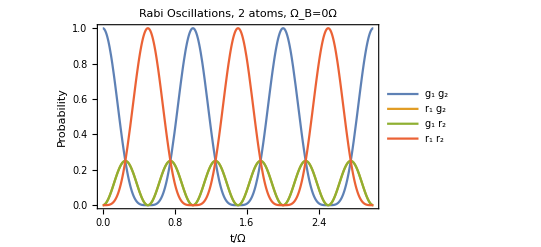

```mathematica
leg = {"g_1 g_2","r_1 g_2","g_1 r_2","r_1 r_2"};
plt=Plot[Evaluate[Abs[soln]^2],{t,0,tmax},PlotLegends->leg,PlotLabel-> Style[StringForm["Rabi Oscillations, `` atoms, Ω_B=``Ω",numAtoms,ΩB/Ω],Black,FontSize->14],LabelStyle->Directive[Black,FontSize->12],Axes-> False,Frame-> {True,True,False,False},FrameLabel->{"t/Ω","Probability"},PlotRange->All]
(*Export[ToString[StringForm["plot_rabi_flop_``atoms_``states_blockaded``.png",numAtoms,numStates,ΩB/Ω]],plt]*)
```

### rabi flopping - 2 or more atoms in uniform blockade

```mathematica
Clear[Ω,Δ];
numStates=2; (*single atom states*)
numAtoms = 4;
atomBasis = IdentityMatrix[numStates];
Hsingle=({{0, Ω/2}, {Ω/2, Δ}});(*assume real Rabi freq.*)

(*construct interaction Hamiltonian*)
Hint = ConstantArray[0,{numAtoms numStates,numAtoms numStates}];
```

```mathematica
(*Build the initial array state and eqs to solve*)
(*Ω=2π;
Δ=0;*)
ΩB[i_,j_]:=10Ω; (*uniform blockade between *)
hamiltonian = HamiltonianProduct[Hsingle,numAtoms]//MatrixForm(*+ BlockadeHamiltonian[numAtoms,BlockadeTerm[#&,ΩB]]*)
```

(0 | Ω/2 | Ω/2 | 0 | Ω/2 | 0 | 0 | 0 | Ω/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
Ω/2 | Δ | 0 | Ω/2 | 0 | Ω/2 | 0 | 0 | 0 | Ω/2 | 0 | 0 | 0 | 0 | 0 | 0
Ω/2 | 0 | Δ | Ω/2 | 0 | 0 | Ω/2 | 0 | 0 | 0 | Ω/2 | 0 | 0 | 0 | 0 | 0
0 | Ω/2 | Ω/2 | 2 Δ | 0 | 0 | 0 | Ω/2 | 0 | 0 | 0 | Ω/2 | 0 | 0 | 0 | 0
Ω/2 | 0 | 0 | 0 | Δ | Ω/2 | Ω/2 | 0 | 0 | 0 | 0 | 0 | Ω/2 | 0 | 0 | 0
0 | Ω/2 | 0 | 0 | Ω/2 | 2 Δ | 0 | Ω/2 | 0 | 0 | 0 | 0 | 0 | Ω/2 | 0 | 0
0 | 0 | Ω/2 | 0 | Ω/2 | 0 | 2 Δ | Ω/2 | 0 | 0 | 0 | 0 | 0 | 0 | Ω/2 | 0
0 | 0 | 0 | Ω/2 | 0 | Ω/2 | Ω/2 | 3 Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Ω/2
Ω/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Δ | Ω/2 | Ω/2 | 0 | Ω/2 | 0 | 0 | 0
0 | Ω/2 | 0 | 0 | 0 | 0 | 0 | 0 | Ω/2 | 2 Δ | 0 | Ω/2 | 0 | Ω/2 | 0 | 0
0 | 0 | Ω/2 | 0 | 0 | 0 | 0 | 0 | Ω/2 | 0 | 2 Δ | Ω/2 | 0 | 0 | Ω/2 | 0
0 | 0 | 0 | Ω/2 | 0 | 0 | 0 | 0 | 0 | Ω/2 | Ω/2 | 3 Δ | 0 | 0 | 0 | Ω/2
0 | 0 | 0 | 0 | Ω/2 | 0 | 0 | 0 | Ω/2 | 0 | 0 | 0 | 2 Δ | Ω/2 | Ω/2 | 0
0 | 0 | 0 | 0 | 0 | Ω/2 | 0 | 0 | 0 | Ω/2 | 0 | 0 | Ω/2 | 3 Δ | 0 | Ω/2
0 | 0 | 0 | 0 | 0 | 0 | Ω/2 | 0 | 0 | 0 | Ω/2 | 0 | Ω/2 | 0 | 3 Δ | Ω/2
0 | 0 | 0 | 0 | 0 | 0 | 0 | Ω/2 | 0 | 0 | 0 | Ω/2 | 0 | Ω/2 | Ω/2 | 4 Δ)

```mathematica
ψ = Array[Subscript[P, #][t]&,numAtoms numStates];
ψ0 = ConstantArray[0,numAtoms numStates];
ψ0[[1]]=1;(*start with all atoms in ground state*)
eqs = {};(*system to solve*)
ics = {};(*initial conditions*)
For[i=1,i<numAtoms numStates+1,i++,
AppendTo[eqs,D[ψ[[i]],t]==ⅈ (hamiltonian.ψ)[[i]]];
AppendTo[ics,(ψ[[i]]/.t->0)==ψ0[[i]]];
];
sys = Flatten@Join[eqs,ics];
{ψ,ψ0,sys};
tmax=3;
{time,soln}= Timing[First@NDSolve[sys, ψ, {t,0,tmax}]];
Print[StringForm["Time to run sim: `` mins",Floor[time/60//N]]];
soln = Table[soln[[i,2]],{i,Range[Length[soln]]}];
```

```mathematica
leg = {"g_1 g_2","r_1 g_2","g_1 r_2","r_1 r_2"};
plt=Plot[Evaluate[Abs[soln]^2],{t,0,tmax},PlotLegends->leg,PlotLabel-> Style[StringForm["Rabi Oscillations, `` atoms, Ω_B=``Ω",numAtoms,ΩB/Ω],Black,FontSize->14],LabelStyle->Directive[Black,FontSize->12],Axes-> False,Frame-> {True,True,False,False},FrameLabel->{"t/Ω","Probability"},PlotRange->All]
```

## multiple Rydberg states

Now we take into account an atom with multiple Rydberg states, including fine structure. We will still assume sufficient detuning on the two-photon transition to merit disregard of the intermediate ladder state.

Start with a 4 level atom: one ground state, three nearby Rydberg states. 
Single atom basis: g, r_α, r_β, r_γ.

```mathematica
Haf1= ({{0, 0, Ωβ1/2, 0}, {0, Δα1, 0, 0}, {Ωβ1/2, 0, Δβ1, 0}, {0, 0, 0, Δγ1}});(*atom + driving field*)
Haf2= ({{0, 0, Ωβ2/2, 0}, {0, Δα2, 0, 0}, {Ωβ2/2, 0, Δβ2, 0}, {0, 0, 0, Δγ2}});
KroneckerProduct[IdentityMatrix[4],Haf1]+KroneckerProduct[Haf2,IdentityMatrix[4]]//MatrixForm
```

(0 | 0 | Ωβ1/2 | 0 | 0 | 0 | 0 | 0 | Ωβ2/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | Δα1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Ωβ2/2 | 0 | 0 | 0 | 0 | 0 | 0
Ωβ1/2 | 0 | Δβ1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Ωβ2/2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | Δγ1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Ωβ2/2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | Δα2 | 0 | Ωβ1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | Δα1+Δα2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | Ωβ1/2 | 0 | Δα2+Δβ1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | Δα2+Δγ1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
Ωβ2/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Δβ2 | 0 | Ωβ1/2 | 0 | 0 | 0 | 0 | 0
0 | Ωβ2/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Δα1+Δβ2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | Ωβ2/2 | 0 | 0 | 0 | 0 | 0 | Ωβ1/2 | 0 | Δβ1+Δβ2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | Ωβ2/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Δβ2+Δγ1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Δγ2 | 0 | Ωβ1/2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Δα1+Δγ2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Ωβ1/2 | 0 | Δβ1+Δγ2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Δγ1+Δγ2)

see if it’s tractable to diagonalize this thing quickly

```mathematica
(*Ωβ=2π;
Δα = Δβ=Δγ=10;*)
Clear[Ωβ,Δβ,Δγ,Δα];
Haf1= ({{0, 0, Ωβ/2, 0}, {0, Δα, 0, 0}, {Ωβ/2, 0, Δβ, 0}, {0, 0, 0, Δγ}});(*atom + driving field*)
```

```mathematica
For[i=2,i<6,i++,
Print[{i, Timing[Eigensystem[HamiltonianProduct[Haf1,i]]][[1]]}]
]
```

{2,0.328125}

$Aborted

Write a routine to prune out the n-excited basis states from the matrix.

```mathematica
Length[HamiltonianProduct[Haf1,2]](*atom-field Ham.*)
```

16

```mathematica
nExcited=2;
excitedList = Flatten@Table[{atomIdcs[[i]],atomIdcs[[j]]},{i,Range[Length[atomIdcs]]},{j,Range[1+i,Length[atomIdcs]]}]
For
```

```mathematica
Clear[i]
```

could build the interaction with brute force. need to generate the basis first.

```mathematica
sbasis={g,α,β,γ};
```

```mathematica
OuterProd[sbasis,sbasis]
```

{{g^2,g α,g β,g γ},{g α,α^2,α β,α γ},{g β,α β,β^2,β γ},{g γ,α γ,β γ,γ^2}}

need outer-product-like function that combines bases. then we can generate the matrix element at each pair of these. probably ask Mark if there is a smarter way to do this simulation.

```mathematica
statecombos={};
For[i=1,i<4,i++,
For[j=1,j<4,j++,
AppendTo[statecombos,{sbasis[[i]],sbasis[[j]]}]
]
]
Table[{sbasis[[i]],sbasis[[j]]},{i,Range[4]},{j,Range[4]}]
```

{{{g,g},{g,α},{g,β},{g,γ}},{{α,g},{α,α},{α,β},{α,γ}},{{β,g},{β,α},{β,β},{β,γ}},{{γ,g},{γ,α},{γ,β},{γ,γ}}}

## misc testing

write recursive function to build multi-atom Hamiltonian by successively combining the single atom subspaces.

```mathematica
(*single atom Hamiltonian with effective basis {g,e}*)
Clear[Ω,Δ];
numStates=2; (*single atom states*)
numAtoms = 2;
H1=({{0, Ω/2}, {Ω/2, Δ}});(*assume real Rabi freq.*)
H2int = ConstantArray[0,{numAtoms numStates,numAtoms numStates}];
H2int[[numAtoms numStates,numAtoms numStates]]=ΩB; (*interaction Hamiltonian*)
```

test building the hamiltonian with kronecker products using only two-level systems

```mathematica
H1=({{0, Ω1/2}, {Ω1/2, Δ1}});
H2=({{0, Ω2/2}, {Ω2/2, Δ2}});
H12 =KroneckerProduct[IdentityMatrix[Length[H2]],H1] + KroneckerProduct[H2,IdentityMatrix[Length[H1]]];
%//MatrixForm
```

(0 | Ω1/2 | Ω2/2 | 0
Ω1/2 | Δ1 | 0 | Ω2/2
Ω2/2 | 0 | Δ2 | Ω1/2
0 | Ω2/2 | Ω1/2 | Δ1+Δ2)

Now add the blockade:

```mathematica
H12int = ConstantArray[0,Dimensions[H12]];
(*H12int[[-1,-1]]=ΩB12;*)
(*H12=H12+H12int;*)
H12//MatrixForm
```

(0 | Ω1/2 | Ω2/2 | 0
Ω1/2 | Δ1 | 0 | Ω2/2
Ω2/2 | 0 | Δ2 | Ω1/2
0 | Ω2/2 | Ω1/2 | Δ1+Δ2)

Now three atoms:

```mathematica
H3=({{0, Ω3/2}, {Ω3/2, Δ3}});
H123=KroneckerProduct[IdentityMatrix[Length[H1]],H12] + KroneckerProduct[H3,IdentityMatrix[Length[H12]]];
H123//MatrixForm
```

(0 | Ω1/2 | Ω2/2 | 0 | Ω3/2 | 0 | 0 | 0
Ω1/2 | Δ1 | 0 | Ω2/2 | 0 | Ω3/2 | 0 | 0
Ω2/2 | 0 | Δ2 | Ω1/2 | 0 | 0 | Ω3/2 | 0
0 | Ω2/2 | Ω1/2 | Δ1+Δ2 | 0 | 0 | 0 | Ω3/2
Ω3/2 | 0 | 0 | 0 | Δ3 | Ω1/2 | Ω2/2 | 0
0 | Ω3/2 | 0 | 0 | Ω1/2 | Δ1+Δ3 | 0 | Ω2/2
0 | 0 | Ω3/2 | 0 | Ω2/2 | 0 | Δ2+Δ3 | Ω1/2
0 | 0 | 0 | Ω3/2 | 0 | Ω2/2 | Ω1/2 | Δ1+Δ2+Δ3)

```mathematica
1,2,3,4,5,6,7,8...
1;2;12;3;13;23;123;4;.. (*essentially counts in binary*)
blockade on 3,5,6,7,9,10,11,12,... no blockade on 2^n; but this is not does
```

Want to generate sequence {0,1,2,{1,2},3,{1,3},{2,3},{1,2,3},4,{1,4},{2,4},{1,2,4},{3,4},{1,3,4},{2,3,4},{1,2,3,4}...};  it’s recursive

with 1 atom it’s {0,1}
2nd atom part is: {0,1,2,{1,2}} which is just taking 2 and combining with each element of previous list then appending onto end of {0,1}
repeat: append {3,{1,3},{2,3},{1,2,3}} to list 2, etc.

```mathematica
listn = {0,1};
n=(Flatten@listn)[[-1]]+1;
AppendTo[listn,n]
AppendTo[listn,Flatten@Table[{listn[[i]],n},{i,Range[2,Length[listn]-1]}]]
```

{0,1,2}

```mathematica
BlockadeHamiltonian[atomNum_]:=Module[
{excitedList={0,1},n,HBlockade},
For[i=1,i<atomNum,i++,
n=(Flatten@excitedList)[[-1]]+1;
AppendTo[excitedList,n];
oldLength = Length[excitedList];
For[j=2,j<oldLength,j++,
AppendTo[excitedList,Flatten@{excitedList[[j]],n}];
];
];

dim = 2^atomNum;
HBlockade = ConstantArray[0,{dim,dim}];
For[k=1,k<dim+1,k++,
atoms = excitedList[[k]];
HBlockade[[k,k]]=If[Length[atoms]>0,BlockadeTerm[atoms],0];
];
HBlockade
];
```

```mathematica
atoms = {1,2,3};
If[Length[atoms]>0,BlockadeTerm[atoms],0]
```

Ω_B^((RowBox[{)+Ω_B^((RowBox[{)+Ω_B^((RowBox[{)

```mathematica
H123+BlockadeHamiltonian[3]//MatrixForm
```

(0 | Ω1/2 | Ω2/2 | 0 | Ω3/2 | 0 | 0 | 0
Ω1/2 | Δ1 | 0 | Ω2/2 | 0 | Ω3/2 | 0 | 0
Ω2/2 | 0 | Δ2 | Ω1/2 | 0 | 0 | Ω3/2 | 0
0 | Ω2/2 | Ω1/2 | Δ1+Δ2+Ω_B^((RowBox[{) | 0 | 0 | 0 | Ω3/2
Ω3/2 | 0 | 0 | 0 | Δ3 | Ω1/2 | Ω2/2 | 0
0 | Ω3/2 | 0 | 0 | Ω1/2 | Δ1+Δ3+Ω_B^((RowBox[{) | 0 | Ω2/2
0 | 0 | Ω3/2 | 0 | Ω2/2 | 0 | Δ2+Δ3+Ω_B^((RowBox[{) | Ω1/2
0 | 0 | 0 | Ω3/2 | 0 | Ω2/2 | Ω1/2 | Δ1+Δ2+Δ3+Ω_B^((RowBox[{)+Ω_B^((RowBox[{)+Ω_B^((RowBox[{))

```mathematica
listn = {0,1};
For[fakeidx=1,fakeidx<4,fakeidx++,
n=(Flatten@listn)[[-1]]+1;
AppendTo[listn,n];
oldLength = Length[listn];
For[fakeidx2=2,fakeidx2<oldLength,fakeidx2++,
AppendTo[listn,Flatten@{listn[[fakeidx2]],n}];
]
]
```

```mathematica
listn
```

{0,1,2,{1,2},3,{1,3},{2,3},{1,2,3},4,{1,4},{2,4},{1,2,4},{3,4},{1,3,4},{2,3,4},{1,2,3,4}}

```mathematica
BuildInteraction
```

```mathematica
dim = Length[listn];
Htestint = ConstantArray[0,{dim,dim}];
For[diag=1,diag<dim,diag++,
Htestint = If[Length[listn[dim]]>0,]
]
```

```mathematica
BlockadeTerm[atomIdcs_]:=Total[Flatten@Table[ΩBString[atomIdcs[[i]],atomIdcs[[j]]],{i,Range[Length[atomIdcs]]},{j,Range[1+i,Length[atomIdcs]]}]]
ΩBString[i_,j_]:=StringForm["Ω_B^(``, ``)",i,j];
```

```mathematica
BlockadeTerm[{1,2,3,4}]
```

Ω_B^((RowBox[{)+Ω_B^((RowBox[{)+Ω_B^((RowBox[{)+Ω_B^((RowBox[{)+Ω_B^((RowBox[{)+Ω_B^((RowBox[{)

```mathematica
alist={1,2,3,4};
Total[Flatten@Table[ΩBString[alist[[i]],alist[[j]]],{i,Range[Length[alist]]},{j,Range[1+i,Length[alist]]}]]
```

Ω_B^((RowBox[{)+Ω_B^((RowBox[{)+Ω_B^((RowBox[{)+Ω_B^((RowBox[{)+Ω_B^((RowBox[{)+Ω_B^((RowBox[{)

```mathematica
BlockadeTerm[]
```

add

```mathematica
Length[1]
```

0

```mathematica
Table[{i,j},{i,Range[1,3]},{j,Range[]}]
```

```mathematica
Flatten@{0,1,2,{{1,2}}}
```

{0,1,2,1,2}

```mathematica
H4=({{0, Ω4/2}, {Ω4/2, Δ4}});
H1234=KroneckerProduct[IdentityMatrix[Length[H1]],H123] + KroneckerProduct[H4,IdentityMatrix[Length[H123]]];
```

```mathematica
H1234//MatrixForm
```

(0 | Ω1/2 | Ω2/2 | 0 | Ω3/2 | 0 | 0 | 0 | Ω4/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
Ω1/2 | Δ1 | 0 | Ω2/2 | 0 | Ω3/2 | 0 | 0 | 0 | Ω4/2 | 0 | 0 | 0 | 0 | 0 | 0
Ω2/2 | 0 | Δ2 | Ω1/2 | 0 | 0 | Ω3/2 | 0 | 0 | 0 | Ω4/2 | 0 | 0 | 0 | 0 | 0
0 | Ω2/2 | Ω1/2 | Δ1+Δ2 | 0 | 0 | 0 | Ω3/2 | 0 | 0 | 0 | Ω4/2 | 0 | 0 | 0 | 0
Ω3/2 | 0 | 0 | 0 | Δ3 | Ω1/2 | Ω2/2 | 0 | 0 | 0 | 0 | 0 | Ω4/2 | 0 | 0 | 0
0 | Ω3/2 | 0 | 0 | Ω1/2 | Δ1+Δ3 | 0 | Ω2/2 | 0 | 0 | 0 | 0 | 0 | Ω4/2 | 0 | 0
0 | 0 | Ω3/2 | 0 | Ω2/2 | 0 | Δ2+Δ3 | Ω1/2 | 0 | 0 | 0 | 0 | 0 | 0 | Ω4/2 | 0
0 | 0 | 0 | Ω3/2 | 0 | Ω2/2 | Ω1/2 | Δ1+Δ2+Δ3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Ω4/2
Ω4/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Δ4 | Ω1/2 | Ω2/2 | 0 | Ω3/2 | 0 | 0 | 0
0 | Ω4/2 | 0 | 0 | 0 | 0 | 0 | 0 | Ω1/2 | Δ1+Δ4 | 0 | Ω2/2 | 0 | Ω3/2 | 0 | 0
0 | 0 | Ω4/2 | 0 | 0 | 0 | 0 | 0 | Ω2/2 | 0 | Δ2+Δ4 | Ω1/2 | 0 | 0 | Ω3/2 | 0
0 | 0 | 0 | Ω4/2 | 0 | 0 | 0 | 0 | 0 | Ω2/2 | Ω1/2 | Δ1+Δ2+Δ4 | 0 | 0 | 0 | Ω3/2
0 | 0 | 0 | 0 | Ω4/2 | 0 | 0 | 0 | Ω3/2 | 0 | 0 | 0 | Δ3+Δ4 | Ω1/2 | Ω2/2 | 0
0 | 0 | 0 | 0 | 0 | Ω4/2 | 0 | 0 | 0 | Ω3/2 | 0 | 0 | Ω1/2 | Δ1+Δ3+Δ4 | 0 | Ω2/2
0 | 0 | 0 | 0 | 0 | 0 | Ω4/2 | 0 | 0 | 0 | Ω3/2 | 0 | Ω2/2 | 0 | Δ2+Δ3+Δ4 | Ω1/2
0 | 0 | 0 | 0 | 0 | 0 | 0 | Ω4/2 | 0 | 0 | 0 | Ω3/2 | 0 | Ω2/2 | Ω1/2 | Δ1+Δ2+Δ3+Δ4)

```mathematica
H5=({{0, Ω5/2}, {Ω5/2, Δ5}});
H12345=KroneckerProduct[IdentityMatrix[Length[H1]],H1234] + KroneckerProduct[H5,IdentityMatrix[Length[H1234]]];
```

```mathematica
H12345[[17;;,17;;]]//MatrixForm
```

(Δ5 | Ω1/2 | Ω2/2 | 0 | Ω3/2 | 0 | 0 | 0 | Ω4/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
Ω1/2 | Δ1+Δ5 | 0 | Ω2/2 | 0 | Ω3/2 | 0 | 0 | 0 | Ω4/2 | 0 | 0 | 0 | 0 | 0 | 0
Ω2/2 | 0 | Δ2+Δ5 | Ω1/2 | 0 | 0 | Ω3/2 | 0 | 0 | 0 | Ω4/2 | 0 | 0 | 0 | 0 | 0
0 | Ω2/2 | Ω1/2 | Δ1+Δ2+Δ5 | 0 | 0 | 0 | Ω3/2 | 0 | 0 | 0 | Ω4/2 | 0 | 0 | 0 | 0
Ω3/2 | 0 | 0 | 0 | Δ3+Δ5 | Ω1/2 | Ω2/2 | 0 | 0 | 0 | 0 | 0 | Ω4/2 | 0 | 0 | 0
0 | Ω3/2 | 0 | 0 | Ω1/2 | Δ1+Δ3+Δ5 | 0 | Ω2/2 | 0 | 0 | 0 | 0 | 0 | Ω4/2 | 0 | 0
0 | 0 | Ω3/2 | 0 | Ω2/2 | 0 | Δ2+Δ3+Δ5 | Ω1/2 | 0 | 0 | 0 | 0 | 0 | 0 | Ω4/2 | 0
0 | 0 | 0 | Ω3/2 | 0 | Ω2/2 | Ω1/2 | Δ1+Δ2+Δ3+Δ5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Ω4/2
Ω4/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Δ4+Δ5 | Ω1/2 | Ω2/2 | 0 | Ω3/2 | 0 | 0 | 0
0 | Ω4/2 | 0 | 0 | 0 | 0 | 0 | 0 | Ω1/2 | Δ1+Δ4+Δ5 | 0 | Ω2/2 | 0 | Ω3/2 | 0 | 0
0 | 0 | Ω4/2 | 0 | 0 | 0 | 0 | 0 | Ω2/2 | 0 | Δ2+Δ4+Δ5 | Ω1/2 | 0 | 0 | Ω3/2 | 0
0 | 0 | 0 | Ω4/2 | 0 | 0 | 0 | 0 | 0 | Ω2/2 | Ω1/2 | Δ1+Δ2+Δ4+Δ5 | 0 | 0 | 0 | Ω3/2
0 | 0 | 0 | 0 | Ω4/2 | 0 | 0 | 0 | Ω3/2 | 0 | 0 | 0 | Δ3+Δ4+Δ5 | Ω1/2 | Ω2/2 | 0
0 | 0 | 0 | 0 | 0 | Ω4/2 | 0 | 0 | 0 | Ω3/2 | 0 | 0 | Ω1/2 | Δ1+Δ3+Δ4+Δ5 | 0 | Ω2/2
0 | 0 | 0 | 0 | 0 | 0 | Ω4/2 | 0 | 0 | 0 | Ω3/2 | 0 | Ω2/2 | 0 | Δ2+Δ3+Δ4+Δ5 | Ω1/2
0 | 0 | 0 | 0 | 0 | 0 | 0 | Ω4/2 | 0 | 0 | 0 | Ω3/2 | 0 | Ω2/2 | Ω1/2 | Δ1+Δ2+Δ3+Δ4+Δ5)

Try to add in the blockade interaction in a straightforward way:

```mathematica
Clear[ΩB];
H1=({{0, Ω1/2}, {Ω1/2, Δ1}});
H2=({{0, Ω2/2}, {Ω2/2, Δ2}});
H12int = ConstantArray[0,{4,4}];
H12int[[4,4]]=ΩB12; 
H12 =KroneckerProduct[IdentityMatrix[Length[H2]],H1] + KroneckerProduct[H2,IdentityMatrix[Length[H1]]]+H12int;
%//MatrixForm
```

(0 | Ω1/2 | Ω2/2 | 0
Ω1/2 | Δ1 | 0 | Ω2/2
Ω2/2 | 0 | Δ2 | Ω1/2
0 | Ω2/2 | Ω1/2 | Δ1+Δ2+ΩB12)

```mathematica
H3=({{0, Ω3/2}, {Ω3/2, Δ3}});
H13 =KroneckerProduct[IdentityMatrix[Length[H3]],H12] + KroneckerProduct[H3,IdentityMatrix[Length[H12]]];
%//MatrixForm
```

(0 | Ω1/2 | Ω2/2 | 0 | Ω3/2 | 0 | 0 | 0
Ω1/2 | Δ1 | 0 | Ω2/2 | 0 | Ω3/2 | 0 | 0
Ω2/2 | 0 | Δ2 | Ω1/2 | 0 | 0 | Ω3/2 | 0
0 | Ω2/2 | Ω1/2 | Δ1+Δ2+ΩB12 | 0 | 0 | 0 | Ω3/2
Ω3/2 | 0 | 0 | 0 | Δ3 | Ω1/2 | Ω2/2 | 0
0 | Ω3/2 | 0 | 0 | Ω1/2 | Δ1+Δ3 | 0 | Ω2/2
0 | 0 | Ω3/2 | 0 | Ω2/2 | 0 | Δ2+Δ3 | Ω1/2
0 | 0 | 0 | Ω3/2 | 0 | Ω2/2 | Ω1/2 | Δ1+Δ2+Δ3+ΩB12)

```mathematica
H13int = H12int = ConstantArray[0,{4,4}];
H13int[[4,4]]=ΩB13; 
H23int = H12int = ConstantArray[0,{4,4}];
H23int[[4,4]]=ΩB23; 
(*H12 =KroneckerProduct[IdentityMatrix[Length[H2]],H1] + KroneckerProduct[H2,IdentityMatrix[Length[H1]]];
%//MatrixForm*)
```

```mathematica
KroneckerProduct[IdentityMatrix[Length[H3]],H13int];
%//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | ΩB13 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | ΩB13)

```mathematica
H3
```

{{0,Ω3/2},{Ω3/2,Δ3}}

```mathematica
H13
```

{{0,Ω1/2,Ω2/2,0,Ω3/2,0,0,0},{Ω1/2,Δ1,0,Ω2/2,0,Ω3/2,0,0},{Ω2/2,0,Δ2,Ω1/2,0,0,Ω3/2,0},{0,Ω2/2,Ω1/2,Δ1+Δ2+ΩB12,0,0,0,Ω3/2},{Ω3/2,0,0,0,Δ3,Ω1/2,Ω2/2,0},{0,Ω3/2,0,0,Ω1/2,Δ1+Δ3,0,Ω2/2},{0,0,Ω3/2,0,Ω2/2,0,Δ2+Δ3,Ω1/2},{0,0,0,Ω3/2,0,Ω2/2,Ω1/2,Δ1+Δ2+Δ3+ΩB12}}

```mathematica
KroneckerDelta[H12int,IdentityMatrix[4]]
```

```mathematica
H13int
```

```mathematica
ΩB
```

0

If we know what the basis is than we will know how to properly build the interaction Hamiltonian. 
{1000,0100,1100,0010,1010}... etc. So writing the states this way, denoting the jth atom in the subspace in its excited (ground) state with a 1 (0) in the jth position of the 4-atom ket, shows that the atoms involved in the blockade are gotten by looking at the non-zero places in the binary representation of the diagonal index. This pattern will change for a more complicated atom but this is a good start.

Now construct such a hamiltonian for an arbitrary number of quantum systems using a function

```mathematica
HamiltonianProduct[hsingle_,volume_ ]:=Module[
{totalham=hsingle},
(*the Hamiltonian describing the combined space of `volume` number of quantum systems with individual Hamiltonian hsingle*)
For[i=1,i<volume,i++,
totalham = KroneckerProduct[IdentityMatrix[Length[ham]],totalham] + KroneckerProduct[ham,IdentityMatrix[Length[totalham]]];
];
totalham
];
```

```mathematica
HamiltonianProduct[Hsingle,4]//MatrixForm
```

(0 | Ω/2 | Ω/2 | 0 | Ω/2 | 0 | 0 | 0 | Ω/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
Ω/2 | Δ | 0 | Ω/2 | 0 | Ω/2 | 0 | 0 | 0 | Ω/2 | 0 | 0 | 0 | 0 | 0 | 0
Ω/2 | 0 | Δ | Ω/2 | 0 | 0 | Ω/2 | 0 | 0 | 0 | Ω/2 | 0 | 0 | 0 | 0 | 0
0 | Ω/2 | Ω/2 | 2 Δ | 0 | 0 | 0 | Ω/2 | 0 | 0 | 0 | Ω/2 | 0 | 0 | 0 | 0
Ω/2 | 0 | 0 | 0 | Δ | Ω/2 | Ω/2 | 0 | 0 | 0 | 0 | 0 | Ω/2 | 0 | 0 | 0
0 | Ω/2 | 0 | 0 | Ω/2 | 2 Δ | 0 | Ω/2 | 0 | 0 | 0 | 0 | 0 | Ω/2 | 0 | 0
0 | 0 | Ω/2 | 0 | Ω/2 | 0 | 2 Δ | Ω/2 | 0 | 0 | 0 | 0 | 0 | 0 | Ω/2 | 0
0 | 0 | 0 | Ω/2 | 0 | Ω/2 | Ω/2 | 3 Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Ω/2
Ω/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Δ | Ω/2 | Ω/2 | 0 | Ω/2 | 0 | 0 | 0
0 | Ω/2 | 0 | 0 | 0 | 0 | 0 | 0 | Ω/2 | 2 Δ | 0 | Ω/2 | 0 | Ω/2 | 0 | 0
0 | 0 | Ω/2 | 0 | 0 | 0 | 0 | 0 | Ω/2 | 0 | 2 Δ | Ω/2 | 0 | 0 | Ω/2 | 0
0 | 0 | 0 | Ω/2 | 0 | 0 | 0 | 0 | 0 | Ω/2 | Ω/2 | 3 Δ | 0 | 0 | 0 | Ω/2
0 | 0 | 0 | 0 | Ω/2 | 0 | 0 | 0 | Ω/2 | 0 | 0 | 0 | 2 Δ | Ω/2 | Ω/2 | 0
0 | 0 | 0 | 0 | 0 | Ω/2 | 0 | 0 | 0 | Ω/2 | 0 | 0 | Ω/2 | 3 Δ | 0 | Ω/2
0 | 0 | 0 | 0 | 0 | 0 | Ω/2 | 0 | 0 | 0 | Ω/2 | 0 | Ω/2 | 0 | 3 Δ | Ω/2
0 | 0 | 0 | 0 | 0 | 0 | 0 | Ω/2 | 0 | 0 | 0 | Ω/2 | 0 | Ω/2 | Ω/2 | 4 Δ)

```mathematica
ham = Hsingle;
volume=4; (*number of quantum system*)
totalham = Hsingle;
For[i=1,i<volume,i++,
totalham = KroneckerProduct[IdentityMatrix[Length[ham]],totalham] + KroneckerProduct[ham,IdentityMatrix[Length[totalham]]];
Print[totalham//MatrixForm]
]
```

(0 | Ω/2 | Ω/2 | 0
Ω/2 | Δ | 0 | Ω/2
Ω/2 | 0 | Δ | Ω/2
0 | Ω/2 | Ω/2 | 2 Δ)

(0 | Ω/2 | Ω/2 | 0 | Ω/2 | 0 | 0 | 0
Ω/2 | Δ | 0 | Ω/2 | 0 | Ω/2 | 0 | 0
Ω/2 | 0 | Δ | Ω/2 | 0 | 0 | Ω/2 | 0
0 | Ω/2 | Ω/2 | 2 Δ | 0 | 0 | 0 | Ω/2
Ω/2 | 0 | 0 | 0 | Δ | Ω/2 | Ω/2 | 0
0 | Ω/2 | 0 | 0 | Ω/2 | 2 Δ | 0 | Ω/2
0 | 0 | Ω/2 | 0 | Ω/2 | 0 | 2 Δ | Ω/2
0 | 0 | 0 | Ω/2 | 0 | Ω/2 | Ω/2 | 3 Δ)

(0 | Ω/2 | Ω/2 | 0 | Ω/2 | 0 | 0 | 0 | Ω/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
Ω/2 | Δ | 0 | Ω/2 | 0 | Ω/2 | 0 | 0 | 0 | Ω/2 | 0 | 0 | 0 | 0 | 0 | 0
Ω/2 | 0 | Δ | Ω/2 | 0 | 0 | Ω/2 | 0 | 0 | 0 | Ω/2 | 0 | 0 | 0 | 0 | 0
0 | Ω/2 | Ω/2 | 2 Δ | 0 | 0 | 0 | Ω/2 | 0 | 0 | 0 | Ω/2 | 0 | 0 | 0 | 0
Ω/2 | 0 | 0 | 0 | Δ | Ω/2 | Ω/2 | 0 | 0 | 0 | 0 | 0 | Ω/2 | 0 | 0 | 0
0 | Ω/2 | 0 | 0 | Ω/2 | 2 Δ | 0 | Ω/2 | 0 | 0 | 0 | 0 | 0 | Ω/2 | 0 | 0
0 | 0 | Ω/2 | 0 | Ω/2 | 0 | 2 Δ | Ω/2 | 0 | 0 | 0 | 0 | 0 | 0 | Ω/2 | 0
0 | 0 | 0 | Ω/2 | 0 | Ω/2 | Ω/2 | 3 Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Ω/2
Ω/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Δ | Ω/2 | Ω/2 | 0 | Ω/2 | 0 | 0 | 0
0 | Ω/2 | 0 | 0 | 0 | 0 | 0 | 0 | Ω/2 | 2 Δ | 0 | Ω/2 | 0 | Ω/2 | 0 | 0
0 | 0 | Ω/2 | 0 | 0 | 0 | 0 | 0 | Ω/2 | 0 | 2 Δ | Ω/2 | 0 | 0 | Ω/2 | 0
0 | 0 | 0 | Ω/2 | 0 | 0 | 0 | 0 | 0 | Ω/2 | Ω/2 | 3 Δ | 0 | 0 | 0 | Ω/2
0 | 0 | 0 | 0 | Ω/2 | 0 | 0 | 0 | Ω/2 | 0 | 0 | 0 | 2 Δ | Ω/2 | Ω/2 | 0
0 | 0 | 0 | 0 | 0 | Ω/2 | 0 | 0 | 0 | Ω/2 | 0 | 0 | Ω/2 | 3 Δ | 0 | Ω/2
0 | 0 | 0 | 0 | 0 | 0 | Ω/2 | 0 | 0 | 0 | Ω/2 | 0 | Ω/2 | 0 | 3 Δ | Ω/2
0 | 0 | 0 | 0 | 0 | 0 | 0 | Ω/2 | 0 | 0 | 0 | Ω/2 | 0 | Ω/2 | Ω/2 | 4 Δ)

Generate the multi-atom blockade interaction matrix

```mathematica
OmegaB[i_,j_]:=KroneckerDelta[i,j]StringForm["ΩB````",i,j]; (*eventually this will be a realistic function*)
```

```mathematica
Bidcs=Table[]
```

ΩB13